# Calculation of eikonal corrections at KE = 100 MeV

9/19/13

## Define Constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.100(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100b.csv"];
```

```mathematica
(*pp100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100b.csv"];*)
```

```mathematica
pp100a=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+I*pp100a[[All,3]]}];
pp100b=Transpose[{pp100b[[All,1]],pp100b[[All,2]]+I*pp100b[[All,3]]}];
```

```mathematica
θpp100=Transpose[{pp100a[[All,1]],(pp100a[[All,2]]+pp100b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp100=θtoq/@θpp100;
```

```mathematica
pn100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn100a.csv"];
pn100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn100b.csv"];
```

```mathematica
(*pn100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn100a.csv"];
pn100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn100b.csv"];*)
```

```mathematica
pn100a=Transpose[{pn100a[[All,1]],pn100a[[All,2]]+I*pn100a[[All,3]]}];
pn100b=Transpose[{pn100b[[All,1]],pn100b[[All,2]]+I*pn100b[[All,3]]}];
```

```mathematica
θpn100=Transpose[{pn100a[[All,1]],(pn100a[[All,2]]+pn100b[[All,2]])/2}];
```

```mathematica
pn100=θtoq/@θpn100;
```

```mathematica
NN100=(pp100+pn100)/2;
f=Interpolation[NN100];
fp=Interpolation[pp100];
fn=Interpolation[pn100];
```

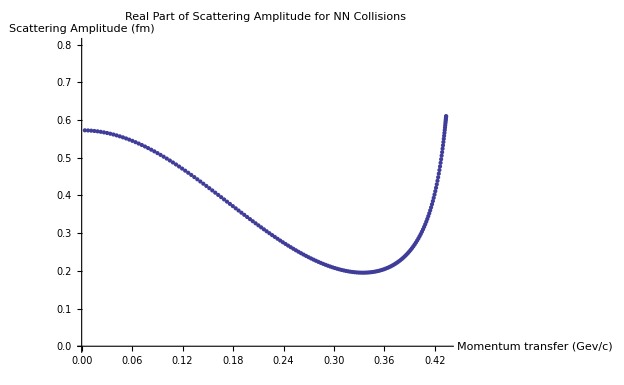

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Re[NN100[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

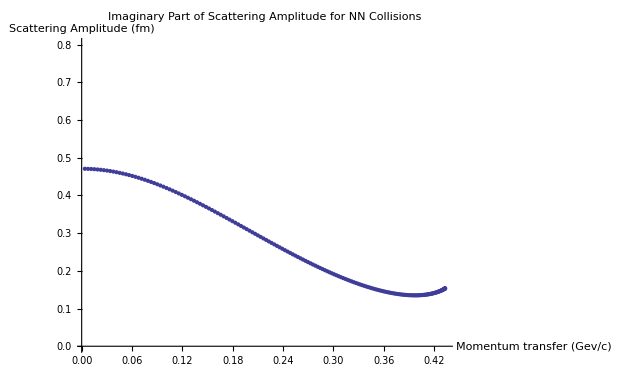

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Im[NN100[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

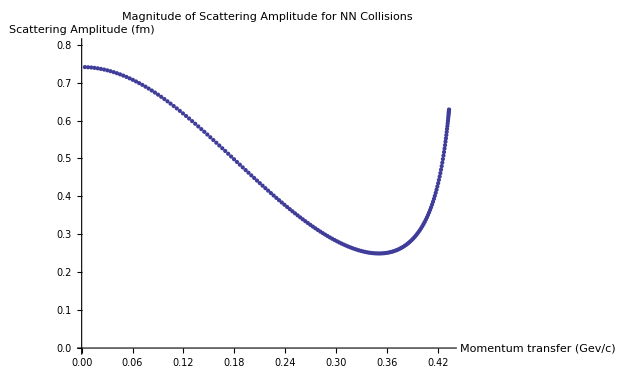

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Abs[NN100[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

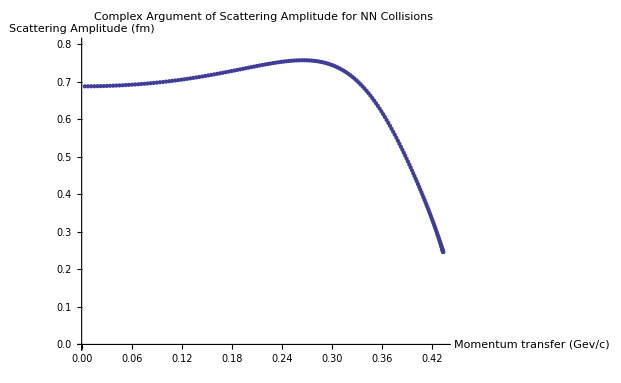

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Arg[NN100[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{a→0.740121,βre→12.3977}

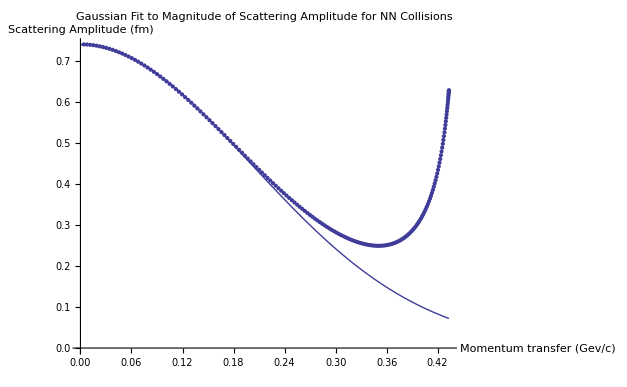

```mathematica
Npts=50;
FindFit[Transpose[{NN100[[1;;Npts,1]],Abs[NN100[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN100[[All,1]],Abs[NN100[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

{ρ→1.21713,βim→-1.26645}

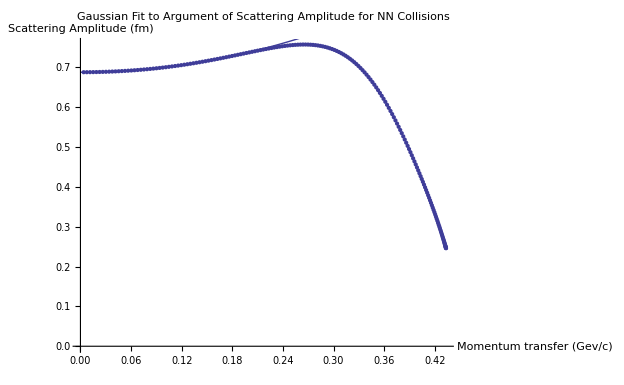

```mathematica
FindFit[Transpose[{NN100[[1;;Npts,1]],Arg[NN100[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN100[[All,1]],Arg[NN100[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.7401208259427848&&ρ==1.217127351734708,{σ,ρ}]
```

{{σ→5.37714,ρ→1.21713}}

Fitted parameters:

```mathematica
σ=5.377143967540269;
ρ=1.217127351734708;
β=12.39772991491029-1.2664454506269087 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

-0.493154+0.489051 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

217.136

```mathematica
ρ0[q_]:=Exp[-B q^2]
```

InterpolatingFunction::dmval: Input value {0.00195861} lies outside the range of data in the interpolating function. Extrapolation will be used.

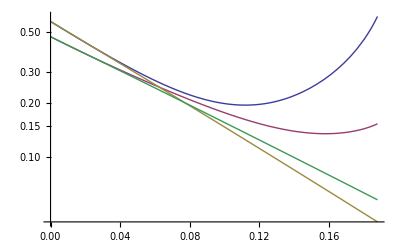

```mathematica
LogPlot[{Re[f[Sqrt[q]]],Im[f[Sqrt[q]]],Re[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]],Im[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]]},{q,0,(2 κ)^2}]
```

InterpolatingFunction::dmval: Input value {0.00195861} lies outside the range of data in the interpolating function. Extrapolation will be used.

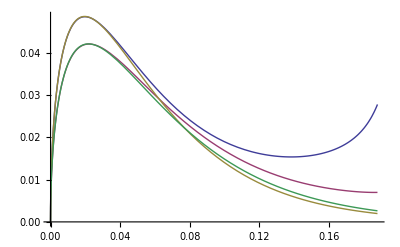

```mathematica
Plot[{Re[Sqrt[q]f[Sqrt[q]] ρ0[Sqrt[q]]],Im[Sqrt[q] f[Sqrt[q]] ρ0[Sqrt[q]]],Re[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]],Im[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]]},{q,0,(2 κ)^2}]
```

```mathematica
Γp=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fp[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
Γn=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fn[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
```

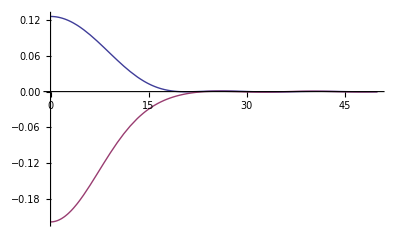

```mathematica
Plot[{Re[Γp[b]],Im[Γp[b]]},{b,0,50},PlotRange->All]
```

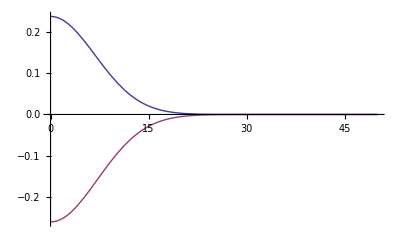

```mathematica
Plot[{Re[σ/ℏc^2 (1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))],Im[σ /ℏc^2(1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))]},{b,0,50},PlotRange->All]
```

```mathematica
Γ[0]
```

Γ[0]

```mathematica
Table[{q,I κ ℏc Exp[q^2B/A] NIntegrate[BesselJ[0,b q](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]},{q,0,.5,.01}]
```

{{0.,0.228887+0.356865 ⅈ},{0.01,0.228524+0.356558 ⅈ},{0.02,0.227442+0.355641 ⅈ},{0.03,0.225672+0.354126 ⅈ},{0.04,0.223257+0.352035 ⅈ},{0.05,0.220249+0.349393 ⅈ},{0.06,0.216706+0.346231 ⅈ},{0.07,0.212685+0.342585 ⅈ},{0.08,0.208234+0.33849 ⅈ},{0.09,0.203398+0.333985 ⅈ},{0.1,0.198216+0.329108 ⅈ},{0.11,0.192723+0.3239 ⅈ},{0.12,0.186956+0.318403 ⅈ},{0.13,0.18096+0.312661 ⅈ},{0.14,0.174784+0.306721 ⅈ},{0.15,0.168492+0.300632 ⅈ},{0.16,0.162151+0.294442 ⅈ},{0.17,0.155837+0.288201 ⅈ},{0.18,0.149622+0.281955 ⅈ},{0.19,0.143573+0.275747 ⅈ},{0.2,0.137743+0.269617 ⅈ},{0.21,0.132172+0.263597 ⅈ},{0.22,0.126881+0.257714 ⅈ},{0.23,0.121878+0.251993 ⅈ},{0.24,0.117161+0.246453 ⅈ},{0.25,0.112725+0.241112 ⅈ},{0.26,0.108565+0.235987 ⅈ},{0.27,0.104688+0.231095 ⅈ},{0.28,0.101109+0.226455 ⅈ},{0.29,0.0978537+0.222084 ⅈ},{0.3,0.0949521+0.218 ⅈ},{0.31,0.0924335+0.214214 ⅈ},{0.32,0.0903163+0.210734 ⅈ},{0.33,0.0885998+0.207559 ⅈ},{0.34,0.0872582+0.204682 ⅈ},{0.35,0.0862379+0.202086 ⅈ},{0.36,0.0854598+0.19975 ⅈ},{0.37,0.0848268+0.197648 ⅈ},{0.38,0.084235+0.195756 ⅈ},{0.39,0.0835878+0.194053 ⅈ},{0.4,0.0828097+0.192527 ⅈ},{0.41,0.0818579+0.191176 ⅈ},{0.42,0.0807297+0.19001 ⅈ},{0.43,0.0794641+0.189047 ⅈ},{0.44,0.0781359+0.188315 ⅈ},{0.45,0.0768456+0.187845 ⅈ},{0.46,0.075704+0.187667 ⅈ},{0.47,0.074816+0.187806 ⅈ},{0.48,0.0742649+0.188277 ⅈ},{0.49,0.0741013+0.189083 ⅈ},{0.5,0.0743371+0.190219 ⅈ}}

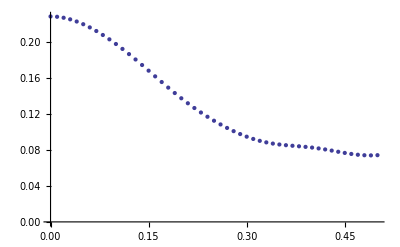

```mathematica
ListPlot[Re[%]]
```

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

217.136

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γ[b])^A),{b,0,50}]]
```

NIntegrate::inumr: The integrand b\ (1 - (1 - Γ[b])^4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 50}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

70.888 Im[(0.+0.0690256 ⅈ) NIntegrate[b BesselJ[0,0] (1-(1-Γ[b])^A),{b,0,50}]]

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]]
```

219.691

```mathematica
μ=mp M/(mp+M);
μab=mp mn/(mp+mn);
```

```mathematica
6 I μ/μab (
```

```mathematica
-I 4.4 ℏc(1+I 0.3)(1.2+.73 I)/2
```

0.47319-0.425871 ⅈ

```mathematica
Sqrt[2.21-I .89]
```

1.51533-0.293665 ⅈ

```mathematica
G[b_]:=-4.4/ℏc^2(1+I .3)/(8 Pi 2.725) Exp[-b^2/(4 2.725)]
```

```mathematica
V[r_]:=I/Pi NIntegrate[D[Log[1-G[b]],b]/Sqrt[b^2-r^2],{b,r,Infinity}]
```

```mathematica
V[0]
```

0.0214817-0.1408 ⅈ

```mathematica
(.437-.070 I)/V[0]
```

0.948608+2.95897 ⅈ

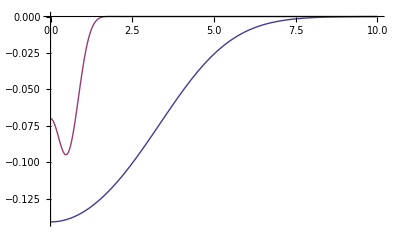

```mathematica
Plot[{Im[V[r]],Im[(0.437-0.070 I) Exp[-(1.612+0.312 I)^2 r^2]]},{r,0,10}]
```

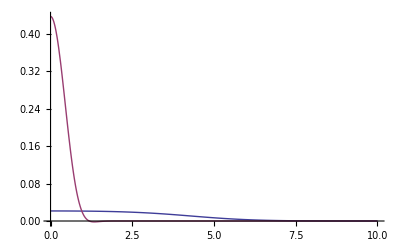

```mathematica
Plot[{Re[V[r]],Re[(0.437-0.070 I) Exp[-(1.612+0.312 I)^2 r^2]]},{r,0,10},PlotRange->All]
```

```mathematica
Integrate[Exp[-z^2 g^2],{z,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(√(g^2)),Re[g^2]>0]

```mathematica
.105659/Sqrt[1-(1/33)^2]
```

0.105708

```mathematica
20/(2.2*10^-6)/(3*10^8)
```

0.030303

```mathematica
105.659*.03
```

3.16977

```mathematica
4*60*60
```

14400

```mathematica
%/Log[4]
```

14400/Log[4]

```mathematica
N[%]
```

10387.4

```mathematica
10387.4/(2.2*10^(-6))
```

4.72155×10^9

```mathematica
%*.105659
```

4.98874×10^8

```mathematica
Exp[I (.0001)]
```

1.+0.0001 ⅈ